### Start choosing the example:

```mathematica
t=11;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6},{1,3,4,S7},{4,3,1,S8},{1,3,2,S9},{2,3,1,S10},{3,4,2,S11},{2,4,3,S12},{2,3,4,S13},{4,3,2,S14},{3,1,2,S15},{2,1,3,S16}}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U2}},Switching Costs→{}|>

```mathematica
Keys@MFGEquations
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,SwitchingCosts,OutRules,InRules,EntryArgs,EntryDataAssociation,jays,NonZeroEntryCurrents,ExitCosts,EqCurrentCompCon,EqTransitionCompCon,EqCompCon,EqAllComp,EqPosCon,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EqEntryIn,EqExitValues,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,EqAllCompRules,EqAllRules,EqAllAll,BoundaryRules,reduced1,reduced2,EqAllAllSimple,RulesEntryIn,RulesExitValues,EqAllAllRules,Nlhs,EqCriticalCase,criticalreduced1,criticalreduced2,Nrhs,EqGeneralCase,TOL}

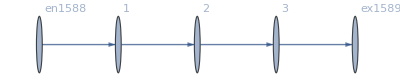

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U2-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

$Aborted

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j14→0,j15→2-1/2,j16→1/2,j17→1/2,j18→2,j19→2-1/2,j20→0,j21→0,j22→0,j23→0,jt24→2-1/2,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2-1/2,jt31→1/2,jt32→1/2,jt33→0,u34→4,u35→4,u36→11/2,u37→5,u38→11/2,u39→2-1/2+4,u40→4,u41→-1/2+11/2,u42→5,u43→11/2|>

```mathematica
Data
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{2,2}},Exit Vertices and Terminal Costs→{{1,4},{3,5}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.18646

FRX1: The Error on the nonlinear terms is 0.0862359

FRX1: The Error on the nonlinear terms is 0.0372694

FRX1: The Error on the nonlinear terms is 0.015763

FRX1: The Error on the nonlinear terms is 0.00663249

FRX1: The Error on the nonlinear terms is 0.00278704

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j14→0,j15→1.95715,j16→2-1.95715,j17→2-1.95715,j18→2,j19→1.95715,j20→0,j21→0,j22→0,j23→0,jt24→1.95715,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.95715,jt31→2-1.95715,jt32→2-1.95715,jt33→0,u34→4.,u35→4,u36→5.03848,u37→5,u38→5.03848,u39→-0.918672+1. 1.95715+1. 4.,u40→4,u41→-1.99564+1. 1.95715+1. 5.03848,u42→5,u43→5.03848|>

```mathematica
FFR
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.167012

FRX1: The Error on the nonlinear terms is 0.073417

FRX1: The Error on the nonlinear terms is 0.0302844

FRX1: The Error on the nonlinear terms is 0.0122286

FRX1: The Error on the nonlinear terms is 0.00490753

FRX1: The Error on the nonlinear terms is 0.0019656

FRX1: The Error on the nonlinear terms is 0.000786723

FRX1: The Error on the nonlinear terms is 0.000314799

FRX1: The Error on the nonlinear terms is 0.00012595

FRX1: The Error on the nonlinear terms is 0.0000503904

<|j14→0,j15→1.91732,j16→2-1.91732,j17→2-1.91732,j18→2,j19→1.91732,j20→0,j21→0,j22→0,j23→0,jt24→1.91732,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.91732,jt31→2-1.91732,jt32→2-1.91732,jt33→0,u34→4.,u35→4,u36→5.07552,u37→5,u38→5.07552,u39→-0.841798+1. 1.91732+1. 4.,u40→4,u41→-1.99284+1. 1.91732+1. 5.07552,u42→5,u43→5.07552|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.125314

FRX1: The Error on the nonlinear terms is 0.0481351

FRX1: The Error on the nonlinear terms is 0.0175282

FRX1: The Error on the nonlinear terms is 0.00626926

FRX1: The Error on the nonlinear terms is 0.00222951

FRX1: The Error on the nonlinear terms is 0.000791349

FRX1: The Error on the nonlinear terms is 0.000280697

FRX1: The Error on the nonlinear terms is 0.0000995417

FRX1: The Error on the nonlinear terms is 0.0000352969

FRX1: The Error on the nonlinear terms is 0.0000125157

<|j14→0,j15→1.82868,j16→2-1.82868,j17→2-1.82868,j18→2,j19→1.82868,j20→0,j21→0,j22→0,j23→0,jt24→1.82868,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.82868,jt31→2-1.82868,jt32→2-1.82868,jt33→0,u34→4.,u35→4,u36→5.15856,u37→5,u38→5.15856,u39→-0.670121+1. 1.82868+1. 4.,u40→4,u41→-1.98724+1. 1.82868+1. 5.15856,u42→5,u43→5.15856|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.00564812

FRX1: The Error on the nonlinear terms is 0.000467942

FRX1: The Error on the nonlinear terms is 0.0000383919

FRX1: The Error on the nonlinear terms is 3.14729×10^-6

FRX1: The Error on the nonlinear terms is 2.57992×10^-7

FRX1: The Error on the nonlinear terms is 2.11482×10^-8

FRX1: The Error on the nonlinear terms is 1.73357×10^-9

FRX1: The Error on the nonlinear terms is 1.42105×10^-10

FRX1: The Error on the nonlinear terms is 1.16491×10^-11

FRX1: The Error on the nonlinear terms is 9.54626×10^-13

<|j14→0,j15→1.54606,j16→2-1.54606,j17→2-1.54606,j18→2,j19→1.54606,j20→0,j21→0,j22→0,j23→0,jt24→1.54606,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.54606,jt31→2-1.54606,jt32→2-1.54606,jt33→0,u34→4.,u35→4,u36→5.44565,u37→5,u38→5.44565,u39→-0.100409+1. 1.54606+1. 4.,u40→4,u41→-1.99172+1. 1.54606+1. 5.44565,u42→5,u43→5.44565|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.86107×10^-15

<|j14→0,j15→3/2,j16→2-3/2,j17→2-3/2,j18→2,j19→3/2,j20→0,j21→0,j22→0,j23→0,jt24→3/2,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→3/2,jt31→2-3/2,jt32→2-3/2,jt33→0,u34→4,u35→4,u36→11/2,u37→5,u38→11/2,u39→3/2+4,u40→4,u41→-2+3/2+11/2,u42→5,u43→11/2|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.0374283

FRX1: The Error on the nonlinear terms is 0.0078923

FRX1: The Error on the nonlinear terms is 0.00170575

FRX1: The Error on the nonlinear terms is 0.000366699

FRX1: The Error on the nonlinear terms is 0.000078923

FRX1: The Error on the nonlinear terms is 0.000016982

FRX1: The Error on the nonlinear terms is 3.65426×10^-6

FRX1: The Error on the nonlinear terms is 7.86327×10^-7

FRX1: The Error on the nonlinear terms is 1.69203×10^-7

FRX1: The Error on the nonlinear terms is 3.64094×10^-8

<|j14→0,j15→1.41188,j16→2-1.41188,j17→2-1.41188,j18→2,j19→1.41188,j20→0,j21→0,j22→0,j23→0,jt24→1.41188,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.41188,jt31→2-1.41188,jt32→2-1.41188,jt33→0,u34→4.,u35→4,u36→5.61741,u37→5,u38→5.61741,u39→0.205527+1. 1.41188+1. 4.,u40→4,u41→-2.02929+1. 1.41188+1. 5.61741,u42→5,u43→5.61741|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.421258

FRX1: The Error on the nonlinear terms is 0.298212

FRX1: The Error on the nonlinear terms is 0.22254

FRX1: The Error on the nonlinear terms is 0.159346

FRX1: The Error on the nonlinear terms is 0.117454

FRX1: The Error on the nonlinear terms is 0.0847023

FRX1: The Error on the nonlinear terms is 0.0620425

FRX1: The Error on the nonlinear terms is 0.0449232

FRX1: The Error on the nonlinear terms is 0.0327987

FRX1: The Error on the nonlinear terms is 0.023801

<|j14→0,j15→1.30174,j16→2-1.30174,j17→2-1.30174,j18→2,j19→1.30174,j20→0,j21→0,j22→0,j23→0,jt24→1.30174,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.30174,jt31→2-1.30174,jt32→2-1.30174,jt33→0,u34→4.,u35→4,u36→5.82373,u37→5,u38→5.82373,u39→0.52199+1. 1.30174+1. 4.,u40→4,u41→-2.12547+1. 1.30174+1. 5.82373,u42→5,u43→5.82373|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.750532

FRX1: The Error on the nonlinear terms is 0.740547

FRX1: The Error on the nonlinear terms is 0.733422

FRX1: The Error on the nonlinear terms is 0.723203

FRX1: The Error on the nonlinear terms is 0.71587

FRX1: The Error on the nonlinear terms is 0.705449

FRX1: The Error on the nonlinear terms is 0.697925

FRX1: The Error on the nonlinear terms is 0.687335

FRX1: The Error on the nonlinear terms is 0.679642

FRX1: The Error on the nonlinear terms is 0.668918

<|j14→0,j15→1.47225,j16→2-1.47225,j17→2-1.47225,j18→2,j19→1.47225,j20→0,j21→0,j22→0,j23→0,jt24→1.47225,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.47225,jt31→2-1.47225,jt32→2-1.47225,jt33→0,u34→4.,u35→4,u36→5.85812,u37→5,u38→5.85812,u39→0.385865+1. 1.47225+1. 4.,u40→4,u41→-2.33037+1. 1.47225+1. 5.85812,u42→5,u43→5.85812|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.750946

FRX1: The Error on the nonlinear terms is 0.741214

FRX1: The Error on the nonlinear terms is 0.73427

FRX1: The Error on the nonlinear terms is 0.724303

FRX1: The Error on the nonlinear terms is 0.717151

FRX1: The Error on the nonlinear terms is 0.706977

FRX1: The Error on the nonlinear terms is 0.699634

FRX1: The Error on the nonlinear terms is 0.689287

FRX1: The Error on the nonlinear terms is 0.681771

FRX1: The Error on the nonlinear terms is 0.671283

FRX1: The Error on the nonlinear terms is 0.663617

FRX1: The Error on the nonlinear terms is 0.653021

FRX1: The Error on the nonlinear terms is 0.645227

FRX1: The Error on the nonlinear terms is 0.634559

FRX1: The Error on the nonlinear terms is 0.626659

FRX1: The Error on the nonlinear terms is 0.615953

FRX1: The Error on the nonlinear terms is 0.607972

FRX1: The Error on the nonlinear terms is 0.597263

FRX1: The Error on the nonlinear terms is 0.589223

FRX1: The Error on the nonlinear terms is 0.578545

FRX1: The Error on the nonlinear terms is 0.570472

FRX1: The Error on the nonlinear terms is 0.559856

FRX1: The Error on the nonlinear terms is 0.551773

FRX1: The Error on the nonlinear terms is 0.541249

FRX1: The Error on the nonlinear terms is 0.533179

FRX1: The Error on the nonlinear terms is 0.522777

FRX1: The Error on the nonlinear terms is 0.514742

FRX1: The Error on the nonlinear terms is 0.504487

FRX1: The Error on the nonlinear terms is 0.496509

FRX1: The Error on the nonlinear terms is 0.486425

FRX1: The Error on the nonlinear terms is 0.478523

FRX1: The Error on the nonlinear terms is 0.468631

FRX1: The Error on the nonlinear terms is 0.460823

FRX1: The Error on the nonlinear terms is 0.451142

FRX1: The Error on the nonlinear terms is 0.443446

FRX1: The Error on the nonlinear terms is 0.433992

FRX1: The Error on the nonlinear terms is 0.426422

FRX1: The Error on the nonlinear terms is 0.417208

FRX1: The Error on the nonlinear terms is 0.409779

FRX1: The Error on the nonlinear terms is 0.400815

FRX1: The Error on the nonlinear terms is 0.393539

FRX1: The Error on the nonlinear terms is 0.384835

FRX1: The Error on the nonlinear terms is 0.377721

FRX1: The Error on the nonlinear terms is 0.369282

FRX1: The Error on the nonlinear terms is 0.36234

FRX1: The Error on the nonlinear terms is 0.354172

FRX1: The Error on the nonlinear terms is 0.347409

FRX1: The Error on the nonlinear terms is 0.339513

FRX1: The Error on the nonlinear terms is 0.332934

FRX1: The Error on the nonlinear terms is 0.325312

FRX1: The Error on the nonlinear terms is 0.318922

FRX1: The Error on the nonlinear terms is 0.311573

FRX1: The Error on the nonlinear terms is 0.305374

FRX1: The Error on the nonlinear terms is 0.298297

FRX1: The Error on the nonlinear terms is 0.292292

FRX1: The Error on the nonlinear terms is 0.285483

FRX1: The Error on the nonlinear terms is 0.279672

FRX1: The Error on the nonlinear terms is 0.273127

FRX1: The Error on the nonlinear terms is 0.267511

FRX1: The Error on the nonlinear terms is 0.261225

FRX1: The Error on the nonlinear terms is 0.255803

FRX1: The Error on the nonlinear terms is 0.249771

FRX1: The Error on the nonlinear terms is 0.24454

FRX1: The Error on the nonlinear terms is 0.238755

FRX1: The Error on the nonlinear terms is 0.233714

FRX1: The Error on the nonlinear terms is 0.228171

FRX1: The Error on the nonlinear terms is 0.223316

FRX1: The Error on the nonlinear terms is 0.218007

FRX1: The Error on the nonlinear terms is 0.213336

FRX1: The Error on the nonlinear terms is 0.208254

FRX1: The Error on the nonlinear terms is 0.203762

FRX1: The Error on the nonlinear terms is 0.198899

FRX1: The Error on the nonlinear terms is 0.194583

FRX1: The Error on the nonlinear terms is 0.189933

FRX1: The Error on the nonlinear terms is 0.185788

FRX1: The Error on the nonlinear terms is 0.181342

FRX1: The Error on the nonlinear terms is 0.177363

FRX1: The Error on the nonlinear terms is 0.173115

FRX1: The Error on the nonlinear terms is 0.169298

FRX1: The Error on the nonlinear terms is 0.165239

FRX1: The Error on the nonlinear terms is 0.161579

FRX1: The Error on the nonlinear terms is 0.157703

FRX1: The Error on the nonlinear terms is 0.154195

FRX1: The Error on the nonlinear terms is 0.150494

FRX1: The Error on the nonlinear terms is 0.147133

FRX1: The Error on the nonlinear terms is 0.1436

FRX1: The Error on the nonlinear terms is 0.140382

FRX1: The Error on the nonlinear terms is 0.137009

FRX1: The Error on the nonlinear terms is 0.133928

FRX1: The Error on the nonlinear terms is 0.13071

FRX1: The Error on the nonlinear terms is 0.127761

FRX1: The Error on the nonlinear terms is 0.124691

FRX1: The Error on the nonlinear terms is 0.12187

FRX1: The Error on the nonlinear terms is 0.118941

FRX1: The Error on the nonlinear terms is 0.116243

FRX1: The Error on the nonlinear terms is 0.113449

FRX1: The Error on the nonlinear terms is 0.110868

FRX1: The Error on the nonlinear terms is 0.108205

FRX1: The Error on the nonlinear terms is 0.105737

FRX1: The Error on the nonlinear terms is 0.103197

FRX1: The Error on the nonlinear terms is 0.100838

FRX1: The Error on the nonlinear terms is 0.0984163

FRX1: The Error on the nonlinear terms is 0.0961623

FRX1: The Error on the nonlinear terms is 0.093853

FRX1: The Error on the nonlinear terms is 0.0916993

FRX1: The Error on the nonlinear terms is 0.0894978

FRX1: The Error on the nonlinear terms is 0.0874402

FRX1: The Error on the nonlinear terms is 0.0853415

FRX1: The Error on the nonlinear terms is 0.0833762

FRX1: The Error on the nonlinear terms is 0.0813756

FRX1: The Error on the nonlinear terms is 0.0794986

FRX1: The Error on the nonlinear terms is 0.0775917

FRX1: The Error on the nonlinear terms is 0.0757993

FRX1: The Error on the nonlinear terms is 0.0739817

FRX1: The Error on the nonlinear terms is 0.0722702

FRX1: The Error on the nonlinear terms is 0.0705379

FRX1: The Error on the nonlinear terms is 0.068904

FRX1: The Error on the nonlinear terms is 0.0672529

FRX1: The Error on the nonlinear terms is 0.0656931

FRX1: The Error on the nonlinear terms is 0.0641195

FRX1: The Error on the nonlinear terms is 0.0626307

FRX1: The Error on the nonlinear terms is 0.061131

FRX1: The Error on the nonlinear terms is 0.05971

FRX1: The Error on the nonlinear terms is 0.0582808

FRX1: The Error on the nonlinear terms is 0.0569246

FRX1: The Error on the nonlinear terms is 0.0555625

FRX1: The Error on the nonlinear terms is 0.0542685

FRX1: The Error on the nonlinear terms is 0.0529704

FRX1: The Error on the nonlinear terms is 0.0517355

FRX1: The Error on the nonlinear terms is 0.0504985

FRX1: The Error on the nonlinear terms is 0.0493203

FRX1: The Error on the nonlinear terms is 0.0481414

FRX1: The Error on the nonlinear terms is 0.0470173

FRX1: The Error on the nonlinear terms is 0.0458938

FRX1: The Error on the nonlinear terms is 0.0448214

FRX1: The Error on the nonlinear terms is 0.0437507

FRX1: The Error on the nonlinear terms is 0.0427276

FRX1: The Error on the nonlinear terms is 0.0417073

FRX1: The Error on the nonlinear terms is 0.0407314

FRX1: The Error on the nonlinear terms is 0.0397591

FRX1: The Error on the nonlinear terms is 0.0388282

FRX1: The Error on the nonlinear terms is 0.0379015

FRX1: The Error on the nonlinear terms is 0.0370136

FRX1: The Error on the nonlinear terms is 0.0361306

FRX1: The Error on the nonlinear terms is 0.0352836

FRX1: The Error on the nonlinear terms is 0.0344421

FRX1: The Error on the nonlinear terms is 0.0336343

FRX1: The Error on the nonlinear terms is 0.0328324

FRX1: The Error on the nonlinear terms is 0.032062

FRX1: The Error on the nonlinear terms is 0.0312977

FRX1: The Error on the nonlinear terms is 0.030563

FRX1: The Error on the nonlinear terms is 0.0298347

FRX1: The Error on the nonlinear terms is 0.029134

FRX1: The Error on the nonlinear terms is 0.0284399

FRX1: The Error on the nonlinear terms is 0.0277717

FRX1: The Error on the nonlinear terms is 0.0271102

FRX1: The Error on the nonlinear terms is 0.026473

FRX1: The Error on the nonlinear terms is 0.0258426

FRX1: The Error on the nonlinear terms is 0.025235

FRX1: The Error on the nonlinear terms is 0.0246342

FRX1: The Error on the nonlinear terms is 0.0240548

FRX1: The Error on the nonlinear terms is 0.0234823

FRX1: The Error on the nonlinear terms is 0.0229297

FRX1: The Error on the nonlinear terms is 0.0223841

FRX1: The Error on the nonlinear terms is 0.0218572

FRX1: The Error on the nonlinear terms is 0.0213372

FRX1: The Error on the nonlinear terms is 0.0208349

FRX1: The Error on the nonlinear terms is 0.0203393

FRX1: The Error on the nonlinear terms is 0.0198603

FRX1: The Error on the nonlinear terms is 0.019388

FRX1: The Error on the nonlinear terms is 0.0189313

FRX1: The Error on the nonlinear terms is 0.0184812

FRX1: The Error on the nonlinear terms is 0.0180457

FRX1: The Error on the nonlinear terms is 0.0176167

FRX1: The Error on the nonlinear terms is 0.0172015

FRX1: The Error on the nonlinear terms is 0.0167926

FRX1: The Error on the nonlinear terms is 0.0163968

FRX1: The Error on the nonlinear terms is 0.0160071

FRX1: The Error on the nonlinear terms is 0.0156297

FRX1: The Error on the nonlinear terms is 0.0152583

FRX1: The Error on the nonlinear terms is 0.0148985

FRX1: The Error on the nonlinear terms is 0.0145445

FRX1: The Error on the nonlinear terms is 0.0142015

FRX1: The Error on the nonlinear terms is 0.0138641

FRX1: The Error on the nonlinear terms is 0.013537

FRX1: The Error on the nonlinear terms is 0.0132155

FRX1: The Error on the nonlinear terms is 0.0129037

FRX1: The Error on the nonlinear terms is 0.0125973

FRX1: The Error on the nonlinear terms is 0.0123

FRX1: The Error on the nonlinear terms is 0.0120079

FRX1: The Error on the nonlinear terms is 0.0117245

FRX1: The Error on the nonlinear terms is 0.0114461

FRX1: The Error on the nonlinear terms is 0.0111759

FRX1: The Error on the nonlinear terms is 0.0109106

FRX1: The Error on the nonlinear terms is 0.010653

FRX1: The Error on the nonlinear terms is 0.0104002

FRX1: The Error on the nonlinear terms is 0.0101546

FRX1: The Error on the nonlinear terms is 0.00991359

FRX1: The Error on the nonlinear terms is 0.00967946

FRX1: The Error on the nonlinear terms is 0.00944977

<|j14→0,j15→1.26023,j16→2-1.26023,j17→2-1.26023,j18→2,j19→1.26023,j20→0,j21→0,j22→0,j23→0,jt24→1.26023,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.26023,jt31→2-1.26023,jt32→2-1.26023,jt33→0,u34→4.,u35→4,u36→5.91082,u37→5,u38→5.91082,u39→0.650587+1. 1.26023+1. 4.,u40→4,u41→-2.17105+1. 1.26023+1. 5.91082,u42→5,u43→5.91082|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.04132

FRX1: The Error on the nonlinear terms is 14.1256

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

«5 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-16.3732+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.771472

FRX1: The Error on the nonlinear terms is 0.774695

FRX1: The Error on the nonlinear terms is 0.777005

FRX1: The Error on the nonlinear terms is 0.780437

FRX1: The Error on the nonlinear terms is 0.782892

FRX1: The Error on the nonlinear terms is 0.786551

FRX1: The Error on the nonlinear terms is 0.789164

FRX1: The Error on the nonlinear terms is 0.793071

FRX1: The Error on the nonlinear terms is 0.795855

FRX1: The Error on the nonlinear terms is 0.800031

<|j14→0,j15→1.50949,j16→2-1.50949,j17→2-1.50949,j18→2,j19→1.50949,j20→0,j21→0,j22→0,j23→0,jt24→1.50949,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.50949,jt31→2-1.50949,jt32→2-1.50949,jt33→0,u34→4.,u35→4,u36→5.86167,u37→5,u38→5.86167,u39→0.352181+1. 1.50949+1. 4.,u40→4,u41→-2.37116+1. 1.50949+1. 5.86167,u42→5,u43→5.86167|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.792915

FRX1: The Error on the nonlinear terms is 0.810472

FRX1: The Error on the nonlinear terms is 0.823116

FRX1: The Error on the nonlinear terms is 0.842587

FRX1: The Error on the nonlinear terms is 0.856473

FRX1: The Error on the nonlinear terms is 0.878233

FRX1: The Error on the nonlinear terms is 0.89359

FRX1: The Error on the nonlinear terms is 0.918126

FRX1: The Error on the nonlinear terms is 0.935248

FRX1: The Error on the nonlinear terms is 0.963202

<|j14→0,j15→1.5552,j16→2-1.5552,j17→2-1.5552,j18→2,j19→1.5552,j20→0,j21→0,j22→0,j23→0,jt24→1.5552,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.5552,jt31→2-1.5552,jt32→2-1.5552,jt33→0,u34→4.,u35→4,u36→5.86869,u37→5,u38→5.86869,u39→0.313492+1. 1.5552+1. 4.,u40→4,u41→-2.42388+1. 1.5552+1. 5.86869,u42→5,u43→5.86869|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.837365

FRX1: The Error on the nonlinear terms is 0.887302

FRX1: The Error on the nonlinear terms is 0.92359

FRX1: The Error on the nonlinear terms is 0.983876

FRX1: The Error on the nonlinear terms is 1.02656

FRX1: The Error on the nonlinear terms is 1.10133

FRX1: The Error on the nonlinear terms is 1.15284

FRX1: The Error on the nonlinear terms is 1.24896

FRX1: The Error on the nonlinear terms is 1.31339

FRX1: The Error on the nonlinear terms is 1.44333

<|j14→0,j15→1.68476,j16→2-1.68476,j17→2-1.68476,j18→2,j19→1.68476,j20→0,j21→0,j22→0,j23→0,jt24→1.68476,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.68476,jt31→2-1.68476,jt32→2-1.68476,jt33→0,u34→4.,u35→4,u36→5.90537,u37→5,u38→5.90537,u39→0.22061+1. 1.68476+1. 4.,u40→4,u41→-2.59013+1. 1.68476+1. 5.90537,u42→5,u43→5.90537|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.984284

FRX1: The Error on the nonlinear terms is 1.16863

FRX1: The Error on the nonlinear terms is 1.30674

FRX1: The Error on the nonlinear terms is 1.60536

FRX1: The Error on the nonlinear terms is 1.81994

FRX1: The Error on the nonlinear terms is 2.40346

FRX1: The Error on the nonlinear terms is 2.87194

FRX1: The Error on the nonlinear terms is 3.24475

FRX1: The Error on the nonlinear terms is 3.70382

FRX1: The Error on the nonlinear terms is 3.70382

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.00694,u37→5,u38→6.00694,u39→0.00693559+1. 2.+1. 4.,u40→4,u41→-4.42578+1. 2.+1. 6.00694,u42→5,u43→6.00694|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.28376

FRX1: The Error on the nonlinear terms is 1.89762

FRX1: The Error on the nonlinear terms is 2.43903

FRX1: The Error on the nonlinear terms is 3.59892

FRX1: The Error on the nonlinear terms is 4.7667

FRX1: The Error on the nonlinear terms is 4.7667

FRX1: The Error on the nonlinear terms is 4.7667

«3 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-5.37057+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.24017

FRX1: The Error on the nonlinear terms is 5.07141

FRX1: The Error on the nonlinear terms is 7.05822

FRX1: The Error on the nonlinear terms is 7.05822

FRX1: The Error on the nonlinear terms is 7.05822

«5 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-6.99091+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.95644

FRX1: The Error on the nonlinear terms is 8.99242

FRX1: The Error on the nonlinear terms is 11.164

FRX1: The Error on the nonlinear terms is 11.164

FRX1: The Error on the nonlinear terms is 11.164

«5 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-9.89413+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 14.698

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

«16 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-16.3732+1. 2.+1. 6.,u42→5,u43→6.|>

### What we this plot for?

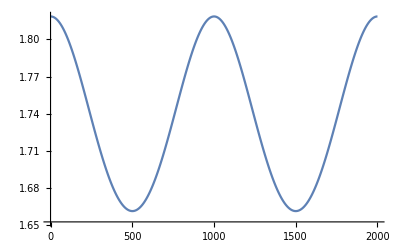

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.